```mathematica
linearEvensSoft=Import["/Users/bennissan/Desktop/ATLAS Research/libsvm/testdata/linearevenssoft.csv","csv"];
linearOddsSoft=Import["/Users/bennissan/Desktop/ATLAS Research/libsvm/testdata/linearoddssoft.csv","csv"];
circleEvensSoft = Import["/Users/bennissan/Desktop/ATLAS Research/libsvm/testdata/circleevenssoft.csv","csv"];
circleOddsSoft=Import["/Users/bennissan/Desktop/ATLAS Research/libsvm/testdata/circleoddssoft.csv","csv"];
twoCircleEvensSoft=Import["/Users/bennissan/Desktop/ATLAS Research/libsvm/testdata/twocircleevenssoft.csv","csv"];
twoCircleOddsSoft=Import["/Users/bennissan/Desktop/ATLAS Research/libsvm/testdata/twocircleoddssoft.csv","csv"];
twoSphereEvensSoft=Import["/Users/bennissan/Desktop/ATLAS Research/libsvm/testdata/twosphereevenssoft.csv","csv"];
twoSphereOddsSoft=Import["/Users/bennissan/Desktop/ATLAS Research/libsvm/testdata/twosphereoddssoft.csv","csv"];
twoSphereEvensSoft100k=Import["/Users/bennissan/Desktop/ATLAS Research/libsvm/testdata/twosphereevenssoft100k.csv","csv"];
twoSphereOddsSoft100k=Import["/Users/bennissan/Desktop/ATLAS Research/libsvm/testdata/twosphereoddssoft100k.csv","csv"];
```

```mathematica
plotWithColors[data_]:=Block[{signal, background,signalPlot, backgroundPlot},
signal = List[];
background = List[];

For[i = 1, i ≤ Length[data],i++,
If[data⟦i⟧⟦3⟧ == 1,AppendTo[signal,Drop[data⟦i⟧,-1]], AppendTo[background,Drop[data⟦i⟧,-1]]]
];

signalPlot = ListPlot[signal,PlotStyle->Blue,PlotRange->{{0,10},{0,10}},AxesLabel->{"Feature 1", "Feature 2"}];
backgroundPlot = ListPlot[background, PlotStyle->Red,PlotRange->{{0,10},{0,10}},AxesLabel->{"Feature 1", "Feature 2"}];

Show[signalPlot, backgroundPlot]
]
```

```mathematica
plotWithColors3D[data_]:=Block[{signal, background,signalPlot, backgroundPlot},
signal = List[];
background = List[];

For[i = 1, i ≤ Length[data],i++,
If[data⟦i⟧⟦4⟧ == 1,AppendTo[signal,Drop[data⟦i⟧,-1]], AppendTo[background,Drop[data⟦i⟧,-1]]]
];

signalPlot = ListPointPlot3D[signal,PlotStyle->Blue,PlotRange->{{0,10},{0,10},{0,10}},AxesLabel->{"Feature 1", "Feature 2","Feature 3"}];
backgroundPlot = ListPointPlot3D[background, PlotStyle->Red,PlotRange->{{0,10},{0,10}},AxesLabel->{"Feature 1", "Feature 2", "Feature 3"}];

Show[signalPlot,backgroundPlot]
]
```

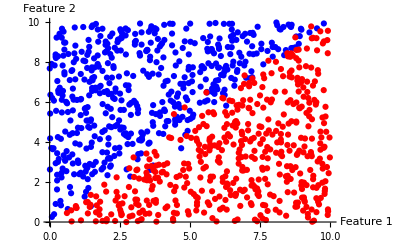

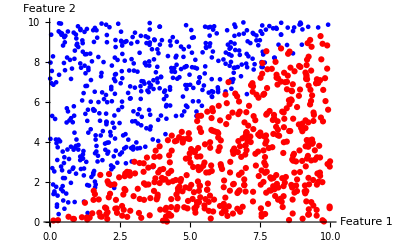

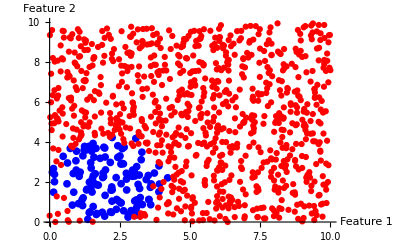

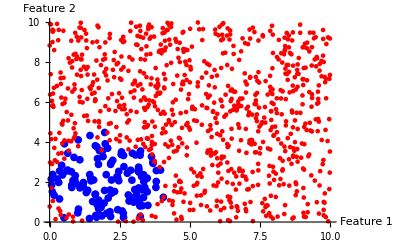

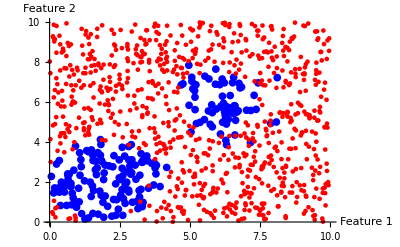

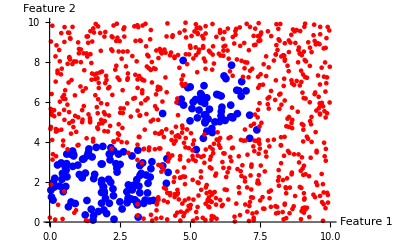

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
plotWithColors[linearEvensSoft]
plotWithColors[linearOddsSoft]
plotWithColors[circleEvensSoft]
plotWithColors[circleOddsSoft]
plotWithColors[twoCircleEvensSoft]
plotWithColors[twoCircleOddsSoft]
plotWithColors3D[twoSphereEvensSoft]
plotWithColors3D[twoSphereOddsSoft]
plotWithColors3D[twoSphereEvensSoft100k]
plotWithColors3D[twoSphereOddsSoft100k]
```